# Common Quantities and Functions

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2016 Eugene d’Eon 
www.eugenedeon.com

## Surface Area of Unit Sphere in d Dimensions

```mathematica
Ω[d_,r_]:=(d π^(d/2)r^(d-1))/Gamma[d/2+1]
```

## Spherical Diffusion Mode in d Dimensions

```mathematica
diffusionMode[v_,d_,r_]:=(2 π)^(-d/2) r^(1-d/2) v^(-1-d/2) BesselK[1/2 (-2+d),r/v]
```

```mathematica
Table[{d,FullSimplify[diffusionMode[v,d,r],Assumptions->v>0&&r>0]},{d,1,3}]//TableForm
```

1 | ⅇ^(-r/v)/(2 v)
2 | BesselK[0,r/v]/(2 π v^2)
3 | ⅇ^(-r/v)/(4 π r v^2)

```mathematica
Integrate[Ω[d,r]diffusionMode[v,d,r],{r,0,Infinity},Assumptions->v>0&&d≥1]
```

1

## Caseology Quantities

### Definitions

```mathematica
CaseN0[c_,v0_]:=1/2 c v0^3 (c/(v0^2-1)-1/v0^2)
```

```mathematica
Casev0[c_?NumericQ]:=FindRoot[c v ArcTanh[1/v]-1,{v,1+10^-10,10^10},Method->"Brent"][[1]][[2]]
```

```mathematica
Casev0[c_,prec_]:=ReplaceAll[Abs[v],First[FindRoot[c v ArcTanh[1/v]-1,{v,2},WorkingPrecision->prec]]];
```

```mathematica
CaseN[c_,v_]:=v (Caseλ[v,c]^2+((π c v)/2)^2)
```

```mathematica
Caseλ[v_,c_]:=1-c v ArcTanh[v]
```

### Approximations

Approximation from [Case and Zweifel 1967]

```mathematica
k0low[c_]:=1-2 E^(-2/c)(1+(4-c)/c E^(-2/c)+(24-12c+c^2)/c^2 E^(-4/c)+(512-384c+72 c^2-3 c^3)/(3 c^3)E^(-6/c));
k0high[c_]:=√(3(1-c))(1-2/5(1-c)-12/175(1-c)^2-2/125(1-c)^3+166/67375(1-c)^4);
Casev0approx[c_]:=If[c>0.56,1/k0high[c],1/k0low[c]]
```

Approximation [d’Eon 2017]

```mathematica
Casev0approx2[c_]:=1/√(1-c^(2.4429445001914587+0.5786368322364553/c-0.021581332427913873 c))
```

### Benchmark Values for Discrete Eigenvalue ν_0

```mathematica
v0BenchTable=TableForm[
Join[{{"α","v_0"}},Map[{N[#],Casev0[#,40]}&,{1/100,5/100,1/10,2/10,3/10,5/10,7/10,8/10,85/100,9/10,95/100,98/100,99/100,995/1000,999/1000,9999/10000,99999/100000,999999/1000000}]]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

α | v_0
0.01 | 1.00000000000000000000000000000009360063
0.05 | 1.000000000000000008496708510583180914518
0.1 | 1.000000004122307593242207339133885345957
0.2 | 1.000090886544380710821109192160326963735
0.3 | 1.002592888793223199142982501642964092168
0.5 | 1.044382033760833484984013906344747760869
0.7 | 1.206804253985286033572144537105448397639
0.8 | 1.407634309062772015890071825808163836056
0.85 | 1.588558625363179696428421317704501663412
0.9 | 1.903204856044847718980561237457780816825
0.95 | 2.635148834268739177311679967586549522622
0.98 | 4.115520476316445421271431792682995753409
0.99 | 5.796729451302002309775836365597598793316
0.995 | 8.181342535857420321730013033380917475302
0.999 | 18.26472572652667373356350462926948043553
0.9999 | 57.73733645201289717419088459805147261345
0.99999 | 182.5749161359718602430336283413298737341
0.999999 | 577.3505001298654062131292059610773432721

### Evaluate Case approximation

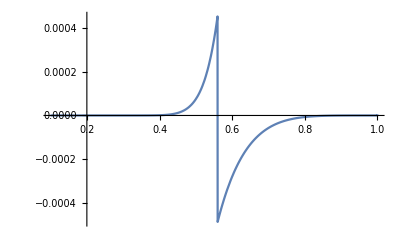

```mathematica
p=Plot[Casev0[c]-Casev0approx[c],{c,0.1,1},PlotRange->All]
```

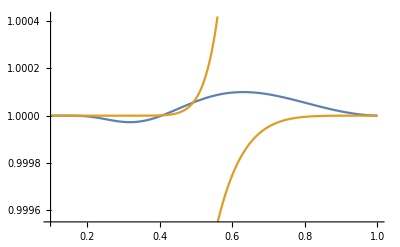

```mathematica
p=Plot[{Casev0[c]/Casev0approx2[c],Casev0[c]/Casev0approx[c]},{c,0.1,1},PlotRange->All]
```